```mathematica
Subscript[Ψ, nlm][r_,θ_,φ_]=SphericalHarmonicY[l,m,θ,φ]*LaguerreL[n-l-1,2l+1,2r/(n Subscript[a, 0])]*E^(-r/(n Subscript[a, 0]))Sqrt[((n-l-1)!/(2n*((n+l)!)))*(2/(n Subscript[a, 0]))^3]*(2r/(n Subscript[a, 0]))^l
```

2^(l+1) ⅇ^(-r/(a_0 n)) √(((-l+n-1)!)/(a_0^3 n^4 (l+n)!)) (r/(a_0 n))^l -l+n-12 l+1(2 r)/(n a_0) Y_l^m(θ,φ)

```mathematica
Subscript[Ψ, nlm](r_,θ_,φ_)=ⅇ^(-r/(Subscript[a, 0] n)) √(((2/(Subscript[a, 0] n))^3 (-l+n-1)!)/(2 n (l+n)!)) ((2 r)/(Subscript[a, 0] n))^l -l+n-12 l+1(2 r)/(n Subscript[a, 0]) Subscript[Y, l]^m(θ,φ)
```

```mathematica
Conjugate[Subscript[Ψ, nlm](r_,θ_,φ_)]
∑_(n=1)^5 ∑_(l=0)^(n-1) ∑_(m=-l)^l Subscript[Ψ, nlm](r_,θ_,φ_)
n(r_)=∫_0^π ∫_0^(2 π) (∑_(n=1)^5 ∑_(l=0)^(n-1) ∑_(m=-l)^l Subscript[Ψ, nlm](r_,θ_,φ_) Conjugate[Subscript[Ψ, nlm](r_,θ_,φ_)])ⅆφⅆθ
Plot[∫_0^π ∫_0^(2 π) (∑_(n=1)^5 ∑_(l=0)^(n-1) ∑_(m=-l)^l Subscript[Ψ, nlm](r_,θ_,φ_) Conjugate[Subscript[Ψ, nlm](r_,θ_,φ_)])ⅆφⅆθ,{r,0,80}]
```

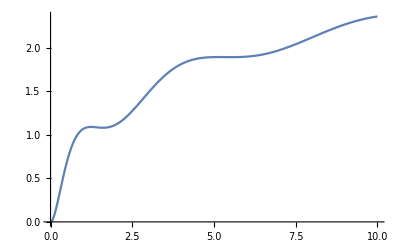

```mathematica
Plot[Integrate[Sum[Abs[SphericalHarmonicY[l,m,θ,φ]*LaguerreL[n-l-1,2l+1,2r/(n)]*E^(-r/(n))Sqrt[((n-l-1)!/(2n*((n+l)!)))*(2/(n))^3]*(2r/(n))^l]^2,{n,1,5},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]*r^2,{r,0,10}]
```

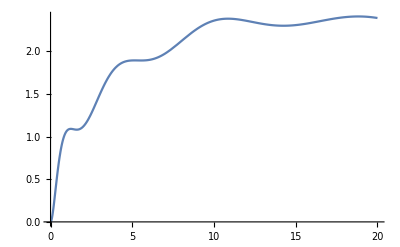

```mathematica
Plot[Integrate[Sum[Abs[SphericalHarmonicY[l,m,θ,φ]*LaguerreL[n-l-1,2l+1,2r/(n)]*E^(-r/(n))Sqrt[((n-l-1)!/(2n*((n+l)!)))*(2/(n))^3]*(2r/(n))^l]^2,{n,1,5},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]*r^2,{r,0,20}]
```

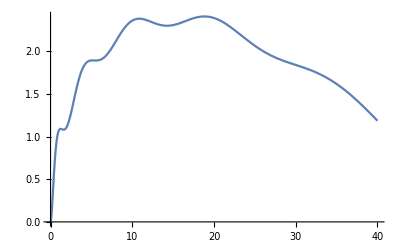

```mathematica
Plot[Integrate[Sum[Abs[SphericalHarmonicY[l,m,θ,φ]*LaguerreL[n-l-1,2l+1,2r/(n)]*E^(-r/(n))Sqrt[((n-l-1)!/(2n*((n+l)!)))*(2/(n))^3]*(2r/(n))^l]^2,{n,1,5},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]*r^2,{r,0,40}]
```

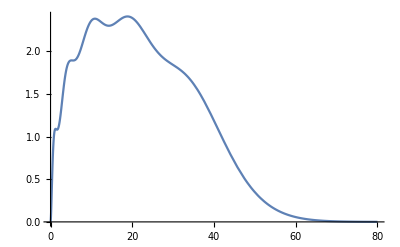

```mathematica
Plot[Integrate[Sum[Abs[SphericalHarmonicY[l,m,θ,φ]*LaguerreL[n-l-1,2l+1,2r/(n)]*E^(-r/(n))Sqrt[((n-l-1)!/(2n*((n+l)!)))*(2/(n))^3]*(2r/(n))^l]^2,{n,1,5},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]*r^2,{r,0,80}]
```

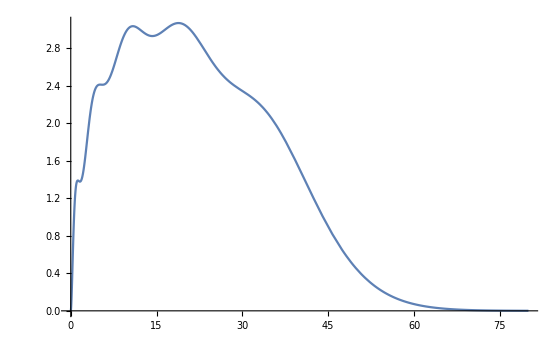

```mathematica
Plot[4/Pi Integrate[Sum[Abs[SphericalHarmonicY[l,m,θ,φ]*LaguerreL[n-l-1,2l+1,2r/(n)]*E^(-r/(n))Sqrt[((n-l-1)!/(2n*((n+l)!)))*(2/(n))^3]*(2r/(n))^l]^2,{n,1,5},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]*r^2,{r,0,80}]
```

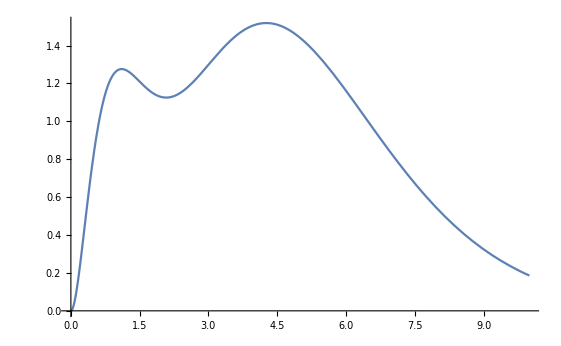

```mathematica
Plot[4/Pi Integrate[Sum[Abs[SphericalHarmonicY[l,m,θ,φ]*LaguerreL[n-l-1,2l+1,2r/(n)]*E^(-r/(n))Sqrt[((n-l-1)!/(2n*((n+l)!)))*(2/(n))^3]*(2r/(n))^l]^2,{n,1,2},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]*r^2,{r,0,10}]
```

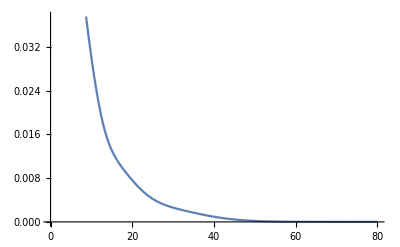

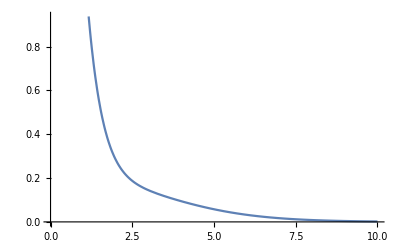

```mathematica
Plot[4/Pi Integrate[Sum[Abs[SphericalHarmonicY[l,m,θ,φ]*LaguerreL[n-l-1,2l+1,2r/(n)]*E^(-r/(n))Sqrt[((n-l-1)!/(2n*((n+l)!)))*(2/(n))^3]*(2r/(n))^l]^2,{n,1,5},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}],{r,0,80}]
Plot[4/Pi Integrate[Sum[Abs[SphericalHarmonicY[l,m,θ,φ]*LaguerreL[n-l-1,2l+1,2r/(n)]*E^(-r/(n))Sqrt[((n-l-1)!/(2n*((n+l)!)))*(2/(n))^3]*(2r/(n))^l]^2,{n,1,2},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}],{r,0,10}]
```

```mathematica
Integrate[4/Pi Integrate[Sum[Abs[SphericalHarmonicY[l,m,θ,φ]*LaguerreL[n-l-1,2l+1,2r/(n)]*E^(-r/(n))Sqrt[((n-l-1)!/(2n*((n+l)!)))*(2/(n))^3]*(2r/(n))^l]^2,{n,1,2},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]*r^2,{r,0,Infinity}]
```

10

```mathematica
Plot[,{r,0,20}]
```